# Track Selection Process

The project is interested in tracks with confidence interval less than 10nm and separations less than 60 nm. In order to find what track properties are relevant to these quantities 746 tracks are analysed and the relationship between different properties, called predictors and confidence interval and separation is explored.

```mathematica
Needs["ErrorBarPlots`"];
rawData = Import[FileNameJoin[{NotebookDirectory[], "corr.csv"}]];
data = Join[#,{#[[10]]/#[[16]] + #[[11]]/#[[17]], (#[[14]]#[[16]]), (#[[15]]#[[17]])}]& /@rawData;
data[[All,9]] = 1/data[[All, 9]];
scoreLabels ={
{1, "ci"},
{2, "sep"},
{3,"σ_OverBar[p12]"},
{4, "σ_OverBar[p1]"},
{5, "σ_OverBar[p2]"},
{6, "σ_p1"},
{7, "σ_p2"},
{8, "Δp_12"},
{9, "C"},
{10, "σ_OverBar[I_1]"},
{11, "σ_OverBar[I_2]"},
{12, "σ_I_1"},
{13, "σ_I_2"},
{14, "T_1"},
{15, "T_2"},
{16, "OverBar[I_1]"},
{17, "OverBar[I_2]"},
{18, "S"},
{19, "Is_1"},
{20, "Is_2"}};
frameTicksStyle =Directive[16, FontColor-> Gray];
plotTextStyle[text_]:=Style[text, FontSize->16, FontColor->Gray];

$PlotTheme = "Default";
cm = 72/2.54;
SetDirectory[NotebookDirectory[]];
AppendTo[$Path, NotebookDirectory[]];
AppendTo[$Path, FileNameJoin[{Directory[], "..", "common"}]];
<<RBM`
<<ErrorBarPlots`
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
size = 9cm;
colorMap = 97;
thesisImages = FileNameJoin[{NotebookDirectory[],"..","..","thesis", "chapters", "img"}];
```

C = (σ_I1+σ_I2)/(|μ_I2+μ_I1|)

S = σ_μ_I1/μ_I1+σ_μ_I2/μ_I2

Δp_12 = (μ_x1- μ_x2)^2+(μ_y1- μ_y2)^2

σ_pi= (∑_(t=1)^T (x_i^t - μ_xi)^2+∑_(t=1)^T (y_i^t- μ_yi)^2)/(T-1)

## Classifying Tracks Lame Way

```mathematica
ev = {Eigenvectors@#, Eigenvalues@#}&@Covariance@Standardize[data[[All, 3;;-1]], Mean, StandardDeviation];
```

```mathematica
Total[ev[[2, 1;;9]]]/Total@ev[[2]]
```

0.967641

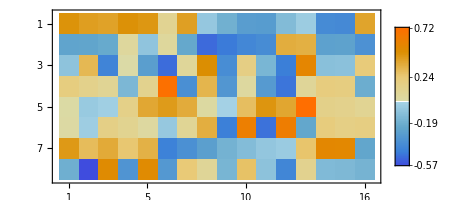

```mathematica
MatrixPlot[ev[[1;;8]], PlotLegends->Automatic, PlotTheme->"Classic"]
```

```mathematica
targets = data[[All,{1, 2}]];
predictors =Standardize[data[[All, 3;;-1]], Mean, StandardDeviation].Transpose[ev[[1]][[1;;9]]];
input = Length@First@predictors;
classes = {unused, used};
output = Length@classes;
```

```mathematica
labelled = #2 ->If[#1[[1]] < 10 && #1[[2]] < 60, used, unused]&@@@ Transpose[{targets, predictors}];
```

```mathematica
samples = 30;
inc = 1./(10 samples);
x = 0.0;
CloseKernels[];LaunchKernels[];
SetSharedVariable[x];
```

```mathematica
AbsoluteTiming[
BinarySerialize[

ParallelTable[
Block[{train, test, r},
{train, test} = TakeDrop[RandomSample[labelled], Floor[0.7 Length[data]]];
Table[
r = {
ClassifierMeasurements[#,train, "F1Score"][used],
ClassifierMeasurements[#,test, "F1Score"][used]
}& @ NetTrain[
NetInitialize[
NetChain[{LinearLayer[hidden],
Tanh,
LinearLayer[output],
SoftmaxLayer[]
},
"Input"-> input,
"Output"-> NetDecoder[{"Class",classes}]],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"->"Normal"}
],
train,
CrossEntropyLossLayer["Target" -> NetEncoder[{"Class", classes}]] ,
Method-> "RMSProp",
MaxTrainingRounds->5000,
TrainingProgressReporting -> None];
CriticalSection[{xlock}, x+= inc];
r,
{hidden, 1, 10}]
],
samples]
] >>"sep-nb.bin"
]
```

{602.583,Null}

```mathematica
Dynamic[Slider[x]]
```

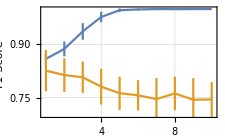

```mathematica
Block[{img, res},
res = BinaryDeserialize[<<"sep-nb.bin"];
img = ErrorListPlot[
Transpose@{Transpose[{Range[1, 10],Mean[#]}], ErrorBar/@StandardDeviation@#}& /@Transpose[res, {2, 3, 1}],
PlotStyle->ColorData[colorMap],
GridLines->Automatic,
Frame-> True,
PlotRange->{{0.9, 10.1}, {0.7, 1.0}},
Joined->True,
FrameTicksStyle-> frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Hidden Units", "F1-Score"}),
PlotLegends->Placed[SwatchLegend[legendStyle/@{"Train", "Test"}, LegendLayout->"Row"], Below],
ImageSize->8cm
];
Export[FileNameJoin[{thesisImages, "track-selection-results.pdf"}], img];
img]
```

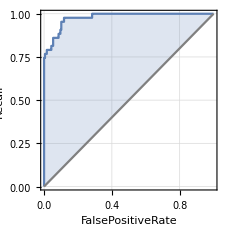

```mathematica
Block[{train, test, m, img},
{train, test} = TakeDrop[RandomSample[labelled], Floor[0.7 Length[data]]];
trained =NetTrain[
NetInitialize[
NetChain[{LinearLayer[1],
Tanh,
LinearLayer[output],
SoftmaxLayer[]
},
"Input"-> input,
"Output"-> NetDecoder[{"Class",classes}]],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"->"Normal"}
],
train,
CrossEntropyLossLayer["Target" -> NetEncoder[{"Class", classes}]] ,
Method-> "RMSProp",
MaxTrainingRounds->1000];
m = ClassifierMeasurements[trained, test]; img = Show[First@m["ROCCurve"][used], ImageSize-> 8cm];
Export[FileNameJoin[{thesisImages, "track-selection-roc.pdf"}], img];
img
]
```

## Training Linear layer and storing it in HDF5 file.

Since the most optimal boundary is by one hidden unit a linear layer is trained and stored in hdf5 file.

```mathematica
data[[index, 3;;-1]]
```

{0.00565226,0.00559155,0.00559813,0.0524534,0.038785,0.176096,0.0840706,131.739,288.053,1235.82,1995.69,89,49,38035.9,76474.,0.00723022}

```mathematica
{0.000177996, 0.00553558, 0.00420424, 0.0522225, 0.0418316, 0.171988, 503.152, 163692, 1758050, 1544260, 17492400, 90,100,38049.7,75884.5,27.4695}
```

```mathematica
targets = data[[All, 1]];
predictors = data[[All, 3;;-1]];
```

Calculate the first 8 PCA components and the mean of the data.

```mathematica
Λ = Inverse[DiagonalMatrix[StandardDeviation[N[predictors]]]];
μ = Mean[predictors];
```

```mathematica
d = Standardize[predictors, Mean, StandardDeviation];
```

```mathematica
P = Eigenvectors[Transpose[d].d][[1;;8]];
```

```mathematica
proj = P.#&/@Standardize[predictors, Mean, StandardDeviation];
```

Project the data and created a labelled data set.

```mathematica
rawLabelled=(#1[[1]] -> If[#1⟦2⟧<10,used,unused]&)/@Transpose[{predictors,targets}];
labelled=(#1⟦1⟧->If[#1⟦2⟧<10,used,unused]&)/@Transpose[{d,targets}];pcaLabelled=(P.#1⟦1⟧->If[#1⟦2⟧<10,used,unused]&)/@Transpose[{d,targets}];
classes={used,unused};
```

Then train a one layer neural network with linear activations.

```mathematica
trained = NetTrain[
NetInitialize[NetChain[{
LinearLayer[2],
SoftmaxLayer[]},
 "Input" -> 8,
 "Output"-> NetDecoder[{"Class", classes}]],
Method-> "Orthogonal"],
pcaLabelled,
CrossEntropyLossLayer["Target"-> NetEncoder[{"Class", classes}]],
Method->"ADAM",
MaxTrainingRounds->5000];
```

```mathematica
ClassifierMeasurements[trained, pcaLabelled, "Accuracy"]
```

0.907507

```mathematica
A = NetExtract[trained, {1, "Weights"}];
B = NetExtract[trained, {1, "Biases"}];
```

```mathematica
w = A.P.Λ;
b = B - w.μ;
```

```mathematica
N[Count[Function[{pair}, (If[#1>#2, used, unused]&@@(w.Keys[pair] +b)) === Values[pair]]/@rawLabelled, True]/Length[labelled]]
```

0.907507

```mathematica
Export["test.h5",{w, b},
{"Datasets", {"layer 0/weights", "layer 0/biases"}},
{"Attributes"-> {"layer 0/weights" -> {"Activation" -> {"linear"}}}}]
```

test.h5

```mathematica
w.{0.00116886,0.0144831,0.0234868,0.127911,0.0968384,0.0505592,690.362,107207,1416330,946830,5839660,79,18,8488.43,18318.8,89.9454} + b
```

{852.418,8810.55}

```mathematica
w.{0.000620027, 0.0166294, 0.0055299, 0.072486, 0.0521689, 0.175838,345.537,290631,916489,1266830,8646140, 20, 90, 26234.9, 54923.5, 27.764} + b
```

{2874.29,5265.96}

```mathematica
{"Datasets", {}}
```

```mathematica
ListPlot[{
#+b&/@Transpose[w.Transpose[Select[data, #[[1]] < 10&][[All, 3;;-1]]]],
#+b&/@Transpose[w.Transpose[Select[data, #[[1]] > 10&][[All, 3;;-1]]]]
} ]
```

### Separation

The correlation plot shows that the separation has highest correlation the predictor Δp_12.

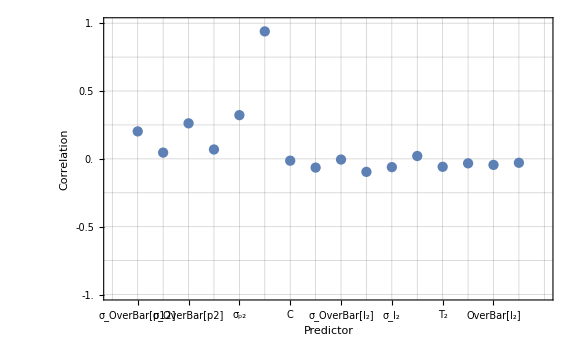

```mathematica
ListPlot[
Correlation[data][[3;;-1, 2]],
Frame -> True,
FrameTicks->{{Range[-1, 1, 0.25],None},{{#[[1]]-2, Rotate[Style[#[[2]], FontSize->16], Pi/2]}&/@scoreLabels[[3;;-1, All]], None}},
FrameLabel->(Style[#, FontSize->16]&/@{"Predictor","Correlation"}),
Axes->True,
PlotRange->{{0, 17}, {-1, 1}},
GridLines->{Range[0, 18],Range[-1, 1, 0.25]},
ImageSize->Large
]
```

In order to evaluate the quality of the predictor Δp_12 the ROC curve is shown and the area under the ROC curve is calculated. The area under the ROC curve is 0.9441.

```mathematica
intROC[
Select[data, #[[2]] < 60&][[All, 8]],
Select[data, #[[2]] ≥ 60&][[All, 8]],
{0,2}
]
```

0.944101

```mathematica
AdjustThresholdBestAcc[targets,data⟦All,8⟧]
```

{0.938338,0.184727}

```mathematica
targets=(If[#1⟦2⟧<60,1,-1]&)/@data;
```

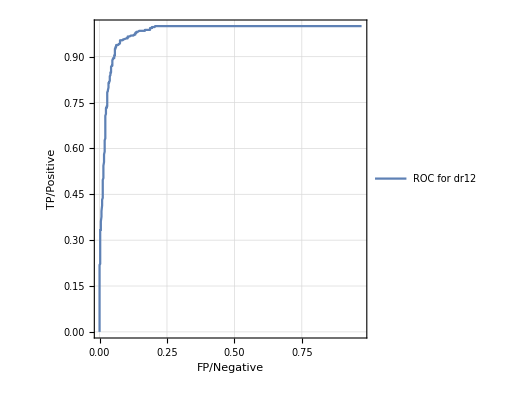

```mathematica
ParametricPlot[
roc[x, #1, #2],
{x, 0, 2},
GridLines->Automatic,
Frame -> True,
FrameLabel->{"FP/Negative","TP/Positive"},
PlotLegends->{"ROC for dr12"}
]&@@ {Select[data, #[[2]]<60&][[All,8]] , Select[data, #[[2]]>60&][[All, 8]]}
```

A threshold of 0.1875 would reject 6.1% of the analyzable tracks which have separation less than 60nm and 93.3% of the analyzable tracks which have separation larger than 60nm. Classifier based on this predictor would have F1 score of 0.926 and  accuracy of 0.935

#### Trying to Use Multiple Predictors

It is possible that more information can be extracted from all the predictors.

```mathematica
targets = data[[All, 2]];
predictors = PrincipalComponents[data[[All, 3;;-1]],
 Method->"Correlation"][[All, 1;;8]];
```

```mathematica
<| Function[sep, sep-> <| 
 "F1Score" -> Function[a, a["F1Score"][used], Listable]@ #,
"Accuracy" -> Function[a, a["Accuracy"], Listable]@#
|> &@ NNExperiment[ Function[pairs, pairs[[2]]->If[pairs[[1]] <sep, used, unused]]/@
Transpose[{targets, predictors}],{1,10}, 30, 3]
] /@ Range[50, 100, 10]|> >> (FileNameJoin[{NotebookDirectory[], "MultiplePredictorsSep.data"}]);
```

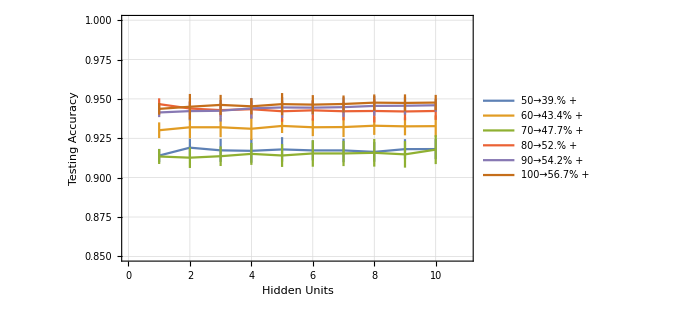
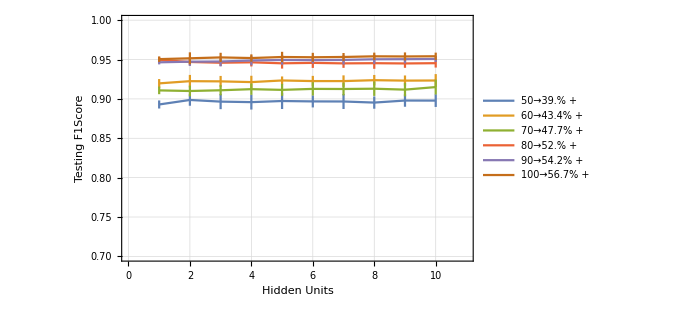

```mathematica
Function[{res,legendLabels},Row[{ErrorListPlot[(ResultSummary[res[#1]["Accuracy"]]⟦2⟧&)/@Range[50,100,10],PlotLegends->legendLabels,PlotRange->{{0,11},{0.85,1}},Frame->True,FrameLabel->{"Hidden Units","Testing Accuracy"},GridLines->Automatic,Joined->True,ImageSize->500],ErrorListPlot[(ResultSummary[res[#1]["F1Score"]]⟦2⟧&)/@Range[50,100,10],PlotLegends->legendLabels,Frame->True,PlotRange->{{0,11},{0.7,1}},FrameLabel->{"Hidden Units","Testing F1Score"},GridLines->Automatic,Joined->True,ImageSize->500]}]]@@{Get[FileNameJoin[{NotebookDirectory[],"MultiplePredictorsSep.data"}]],(#1->ToString[Round[N[Count[targets,u_/;u<#1]/Length[targets]] 100,0.1]]<>"% +"&)/@Range[50,100,10]}
```

The results from the classification of multiple predictors with neural network shows that non-linear boundaries do not improve the testing accuracy of the classifier and therefore linear classification can be assumed the be optimal. The testing accuracy of linear classifier for split at 60nm is 0.930 and f1 score measured on the testing set is 0.919. Comparing these results to the results of the classifier based on predictor Δp_12 and manually adjusted threshold, which has  F1 score of 0.926 and  accuracy of 0.935 shows that there is no improvement to the classification quality, when using multiple predictors.

### Classifier Performance

Using the thresholds derived in the previous sections

```mathematica
N[OneDClassifierMeasure[{0.024, 0.1875}, Select[data, #[[2]]<60&&#[[1]]<10&][[All, {18,8}]],
Select[data, #[[2]]≥60||#[[1]]≥10&][[All, {18,8}]]]]
```

{0.724551,0.876676}

## Classifying Tracks Normal Way

Some Helper Functions Below

```mathematica
hiddenStates = Join[Range[1, 10], Range[12, 20, 2], Range[25, 30, 5]];
TransformLabelledData[data_, trf_]:= #1->#2 &@@@ Transpose[{trf@Keys@data, Values@data}];
SplitTrainTestData[data_]:= TakeDrop[RandomSample[data], Floor[0.7 Length@data]];
acTransform[d_]:=Transpose[(1.9(#3- #2)/(#1-#2)-0.95)&@@{Max@#,Min@#, #}&/@ Transpose[d]];
RunNNExperiment[data_]:= Table[
Function[{train, test},
CloseKernels[];LaunchKernels[8];
ParallelTable[
{ClassifierMeasurements[#, train, "F1Score"][yes], ClassifierMeasurements[#, test, "F1Score"][yes]}&@NetTrain[NetInitialize[NetChain[{
LinearLayer[hu],
Tanh,
LinearLayer[2],
SoftmaxLayer[]},
"Input"-> Length@First@Keys@train,
"Output" -> NetDecoder[{"Class", Union@Values@train}]
],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}],
train,
Method->"ADAM",
LossFunction->CrossEntropyLossLayer["Index"],
MaxTrainingRounds->10000,
TrainingProgressReporting->None
],
{hu,hiddenStates}]
] @@ SplitTrainTestData[data],
10];
```

## Representation

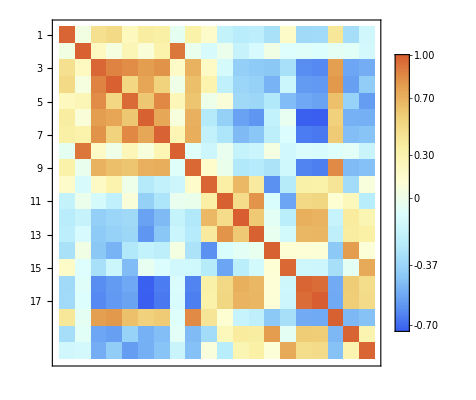

```mathematica
MatrixPlot[Correlation[data],
FrameTicks->{{Range[1, 18],scoreLabels}, { None, scoreLabels}},
PlotLegends->Automatic,
ColorFunction->"LightTemperatureMap"
]
```

```mathematica
usedScores = {3, 4, 5,6, 7, 8, 9, 18, 19, 20};
```

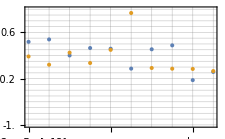

```mathematica
Block[{img, xticks},
xticks = Transpose[{Range[1,10],scoreLabels⟦usedScores,2⟧}];
img = ListPlot[Transpose[{Range[1, 10],#}]&/@Correlation[data]⟦{1, 2},usedScores⟧,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[-1, 1, 0.2], None},{xticks, None}},
PlotRange->{{1, 10}, {-1, 1}},
PlotRangePadding->Scaled[0.05],
GridLines->{Range[1,10],Range[-1, 1, 0.1]},
PlotLegends->Placed[legendStyle/@{"Confidence Interval","Separation"} ,Below],
ImageSize->8cm];
Export[FileNameJoin[{thesisImages, "new-process_track-select_correlation.pdf"}], img];
img]
```

```mathematica
labelled=(#1⟦usedScores⟧->If[#1⟦1⟧<10&&#1⟦2⟧<60,yes,no]&)/@data;
```

## Compression

The data is scaled so that in each dimension the largest values is 1 and smallest is - 1.

```mathematica
trData = TransformLabelledData[labelled, acTransform];
```

Split the data into testing and training samples. This is done to check whether the auto-encoder over-fits the data or not.

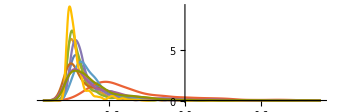

```mathematica
Block[{img},
img = SmoothHistogram[Transpose@Keys@trData,
PlotRange->All,
TicksStyle->frameTicksStyle,
ImageSize->12cm,
AspectRatio->1/3];
Export[FileNameJoin[{thesisImages, "new-process_track-select_ac-data-spread.pdf"}],img];
img]
```

### AutoEncoder

```mathematica
compressionError = Function[data,
Block[{train, test,
acEpoch, epoch, lrate, momentum, RBMdata, rbms, tdata, trained,
ev
},
acEpoch = 10000;
epoch = 5000;
lrate = 0.01;
momentum = 0.9;
RBMdata = <| 10 -> train|>;
rbms = <||>;

{train, test} = Keys/@SplitTrainTestData[data];

rbms[8] = RBMTrain[8, RBMdata[10],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[8] = RBMHiddenExpectation[rbms[8], RBMdata[10]];

rbms[6] = RBMTrain[6, RBMdata[8],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[6] = RBMHiddenExpectation[rbms[6], RBMdata[8]];

rbms[4] = RBMTrain[4, RBMdata[6],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[4] = RBMHiddenExpectation[rbms[4], RBMdata[6]];

rbms[2] = RBMTrain[2, RBMdata[4],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];

tdata=(#1[[1]]->#1[[2]]&)/@Transpose[{RBMdata[10],RBMdata[10]}];
trained = <||>;

trained[2] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4], rbms[2]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None
];

trained[4] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None
];

trained[6] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8],rbms[6]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None
];

ev = Eigenvectors@Covariance@train;

{
Function[c,
Function[{acTrain, acTest},
{Mean[#.#&/@ (acTrain - trained[c]/@acTrain)],Mean[#.#&/@ (acTest - trained[c]/@acTest)]}
] @@ {train, test}
]/@ {2,4,6},
Function[c,
Function[{acTrain, acTest},
{Mean[#.#&/@ (acTrain -Transpose[ Transpose[
Transpose[(Transpose[acTrain] - #)].Transpose[ev[[1;;c]]].ev[[1;;c]]
] + # &@Mean[acTrain]])],
Mean[#.#&/@ (acTest - Transpose[
Transpose[
Transpose[(Transpose@acTest - #)].Transpose[ev[[1;;c]]].ev[[1;;c]] 
]+ # &@ Mean[acTest]])]}
] @@ {train, test}
] /@ Range[2,6,2]
}
]
]@ trData;
```

### Comparison

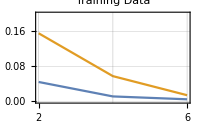
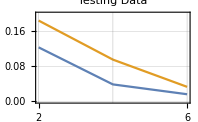

```mathematica
Block[{xticks, yticks, xrange,yrange, img},
xticks={2, 4, 6};
yticks = Automatic;
xrange = {2,6};
yrange = {0.0, 0.2};
img = Function[{resTrain,resTest},
Column[{
Row[{
ListLinePlot[Transpose[{Range[2, 6,2],#}]&/@resTrain,
PlotLabel->plotLabelStyle["Training Data"],
Frame -> True,
FrameLabel->{
{frameLabelStyle@Rotate["ℰ", -Pi/2], None},
{frameLabelStyle@"Dimensionality", None}},
PlotRange->{xrange,yrange},
PlotRangePadding->Scaled[0.05],
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{yticks,None}, {xticks,None}},
GridLines->{xticks, yticks},
ImageSize->7cm,
PlotStyle->ColorData[colorMap]
],

ListLinePlot[Transpose[{Range[2, 6,2],#}]&/@resTest,
PlotLabel->plotLabelStyle["Testing Data"],
Frame -> True,
FrameLabel->{
{frameLabelStyle@Rotate["ℰ", -Pi/2], None},
{frameLabelStyle@"Dimensionality", None}},
PlotRange->{xrange,yrange},
PlotRangePadding->Scaled[0.05],
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{yticks,None}, {xticks,None}},
GridLines->{xticks, yticks},
ImageSize->7cm,
PlotStyle->ColorData[colorMap]
]
}],
SwatchLegend[ColorData[colorMap]/@{1, 2}, legendStyle/@{"AC", "PCA"}, LegendLayout->"Row"]
},
Alignment->Center
]
] @@ Transpose[compressionError, {2,3,1}];
Export[FileNameJoin[{thesisImages, "new-process_track-select_reconstruction-error.pdf"}], img];
img
]
```

```mathematica
Transpose[compressionError, {2,3,1}]
```

{{{0.0443254,0.0112521,0.00468108},{0.155806,0.0577063,0.0140301}},{{0.123544,0.0387784,0.0162553},{0.184891,0.0955429,0.0331724}}}

## Classification

```mathematica
Total[#[[1;;2]]]/Total[#]&@Eigenvalues@Covariance@Standardize@Keys@labelled
```

```mathematica
Function[rawdata,
Block[{acEpoch, epoch, lrate, momentum, RBMdata, rbms, encoder, trData, trained, tdata},
trData = TransformLabelledData[rawdata, acTransform];
acEpoch = 10000;
epoch = 5000;
lrate = 0.01;
momentum = 0.9;
RBMdata = <| 10 -> Keys@trData|>;
rbms = <||>;

(* Train RBMS *)
rbms[8] = RBMTrain[8, RBMdata[10],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[8] = RBMHiddenExpectation[rbms[8], RBMdata[10]];

rbms[6] = RBMTrain[6, RBMdata[8],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[6] = RBMHiddenExpectation[rbms[6], RBMdata[8]];

rbms[4] = RBMTrain[4, RBMdata[6],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];
RBMdata[4] = RBMHiddenExpectation[rbms[4], RBMdata[6]];

rbms[2] = RBMTrain[2, RBMdata[4],
LearningRate-> lrate,
Momentum-> momentum,
MaxTrainingRounds-> epoch];

(* Train autoencoders with GD *)
tdata=(#1[[1]]->#1[[2]]&)/@Transpose[{RBMdata[10],RBMdata[10]}];

trained[6] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8], rbms[6]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None];

trained[4] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None];

trained[2] = NetTrain[
NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4], rbms[2]}], "Input" -> Length@Keys@First@tdata],
tdata,
Method-> "ADAM",
MaxTrainingRounds->acEpoch,
LossFunction->MeanSquaredLossLayer[],
TrainingProgressReporting->None];

(* Train Classifiers *)
Function[encoder,
BinarySerialize@RunNNExperiment@TransformLabelledData[trData, Standardize[encoder/@#]&] >> "cisep-revscore3-ac6-standardize.bin";
] @ NetTake[#, (Length@#)/2]&@trained[6];

Function[encoder,
BinarySerialize@RunNNExperiment@TransformLabelledData[trData, Standardize[encoder/@#]&] >> "cisep-revscore3-ac4-standardize.bin";
] @ NetTake[#, (Length@#)/2]&@trained[4];

Function[encoder,
BinarySerialize@RunNNExperiment@TransformLabelledData[trData, Standardize[encoder/@#]&] >> "cisep-revscore3-ac2-standardize.bin";
] @ NetTake[#, (Length@#)/2]&@trained[2];

]
]@ labelled
```

```mathematica
Function[rawdata,
Block[{slabelled,comp},
slabelled=TransformLabelledData[rawdata,Standardize];comp=Eigenvectors[Covariance[Keys[slabelled]]];

BinarySerialize@RunNNExperiment@TransformLabelledData[slabelled,Standardize[#1.Transpose[comp⟦1;;6⟧]]&]>>"cisep-revscore3-pca6-standardize.bin";

BinarySerialize@RunNNExperiment@TransformLabelledData[slabelled,Standardize[#1.Transpose[comp⟦1;;2⟧]]&]>>"cisep-revscore3-pca2-standardize.bin";
]
]@ labelled;
```

```mathematica
BinarySerialize@RunNNExperiment@TransformLabelledData[labelled,Standardize[#1]&]>>"cisep-revscore3-raw-standardize.bin";
```

```mathematica
resultAC = {BinaryDeserialize[<<"cisep-revscore3-ac2-standardize.bin"],
BinaryDeserialize[<<"cisep-revscore3-ac4-standardize.bin"],
BinaryDeserialize[<<"cisep-revscore3-ac6-standardize.bin"]};
```

```mathematica
resultPCA = {BinaryDeserialize[<<"cisep-revscore3-pca2-standardize.bin"],
BinaryDeserialize[<<"cisep-revscore3-pca4-standardize.bin"],
BinaryDeserialize[<<"cisep-revscore3-pca6-standardize.bin"]};
```

```mathematica
resultRAW = BinaryDeserialize[<<"cisep-revscore3-raw-standardize.bin"];
```

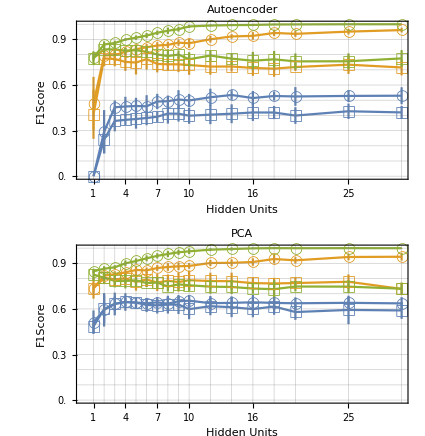

```mathematica
Block[{img},
img = Column[{
GraphicsColumn[{ErrorListPlot[
Flatten[
Transpose[{Transpose[{hiddenStates,#}]&/@Transpose@Mean[#], Map[ErrorBar,(Transpose@StandardDeviation[#]),{2}]},{3,1,2}]&/@resultAC, 1
],
Joined-> True,
PlotRange->{{Min[hiddenStates], Max[hiddenStates]}, {0, 1}},
PlotRangePadding->Scaled[.05],
PlotStyle-> (ColorData[colorMap]/@Flatten[Table[#,2]&/@Range[1, Length[resultAC]], 1]),
PlotMarkers->{{"○",15}, {"□",15}},
Frame-> True,
GridLines->{hiddenStates, Range[0.0, 1., 0.1]},
FrameTicks->{{Range[0.0, 1., 0.1],None},{hiddenStates, None}},
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Hidden Units", "F1Score"}),
PlotLabel->plotLabelStyle@"Autoencoder",
AspectRatio->1/2
],

ErrorListPlot[
Flatten[
Transpose[{Transpose[{hiddenStates,#}]&/@Transpose@Mean[#], Map[ErrorBar,(Transpose@StandardDeviation[#]),{2}]},{3,1,2}]&/@resultPCA, 1
],
Joined-> True,
PlotRange->{{Min[hiddenStates], Max[hiddenStates]}, {0, 1}},
PlotRangePadding->Scaled[.05],
PlotStyle-> (ColorData[colorMap]/@Flatten[Table[#,2]&/@Range[1, Length[resultPCA]], 1]),
PlotMarkers->{{"○",15}, {"□",15}},
Frame-> True,
GridLines->{hiddenStates, Range[0.0, 1., 0.1]},
FrameTicks->{{Range[0.0, 1., 0.1],None},{hiddenStates, None}},
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Hidden Units", "F1Score"}),
PlotLabel->plotLabelStyle@"PCA",
AspectRatio->1/2
]},
Spacings->{0, 10},
ImageSize-> 15cm],
SwatchLegend[ColorData[colorMap]/@ Range[1, 3],
legendStyle/@{"Dim: 2","Dim: 4", "Dim: 6"},
LegendLayout-> "Row"],
LineLegend[ColorData[colorMap]/@{1,1}, legendStyle/@{"Train", "Test"}, LegendMarkers->{{"○",15}, {"□",15}}, LegendLayout->"Row"]
},
Alignment->Center];
Export[FileNameJoin[{thesisImages,"new-process_track-select_ac-pca.pdf"}], img];
img]
```

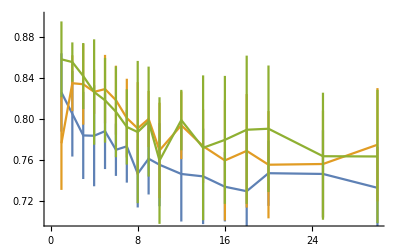

```mathematica
ErrorListPlot[
Transpose[{Transpose[{hiddenStates,Mean[#]}], ErrorBar/@StandardDeviation[#]}]&/@{resultPCA[[3, All, All, 2]],resultAC[[3, All, All, 2]],resultRAW[[All, All, 2]]},
Joined-> True,
PlotRange->{{Min[hiddenStates], Max[hiddenStates]}, {0.7, 0.9}},
PlotRangePadding->Scaled[.05],
PlotStyle-> (ColorData[colorMap]/@{1, 2, 3})
]
```

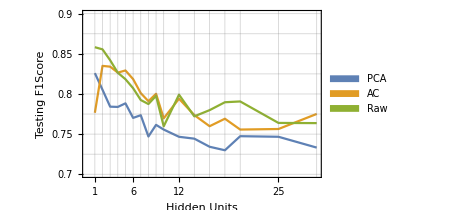

```mathematica
Block[{img},
img = Show[
ListPlot[
Transpose[{hiddenStates,Mean[#]}]&/@{resultPCA[[3, All, All, 2]],resultAC[[3, All, All, 2]],resultRAW[[All, All, 2]]},
Joined-> True,
PlotRange->{{Min[hiddenStates], Max[hiddenStates]}, {0.7, 0.9}},
PlotRangePadding->Scaled[.05],
PlotStyle-> (ColorData[colorMap]/@{1, 2, 3}),
Frame-> True,
GridLines->{hiddenStates, Range[0.7, 0.9, 0.025]},
FrameTicks->{{Range[0.7, 0.9, 0.025],None},{hiddenStates, None}},
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Hidden Units", "Testing F1Score"}),
PlotLegends->Placed[SwatchLegend[legendStyle/@{"PCA", "AC", "Raw"}],Below]
],
ImageSize->12cm
];
Export[FileNameJoin[{thesisImages,"new-process_track-select_summary-f1.pdf"}], img];
img]
```

```mathematica
{train, test} = SplitTrainTestData@TransformLabelledData[labelled, Standardize];
```

```mathematica
cls = NetTrain[
NetInitialize[
NetChain[{LinearLayer[1], Tanh, LinearLayer[2], SoftmaxLayer[]},
"Input"-> Length@Keys@First@train,
"Output" -> NetDecoder[{"Class", Union@Values@train}]
],
Method-> {"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}
],
train,
Method-> "ADAM",
MaxTrainingRounds->3000,
LossFunction->CrossEntropyLossLayer["Index"]
];
```

```mathematica
m = ClassifierMeasurements[cls, test];
```

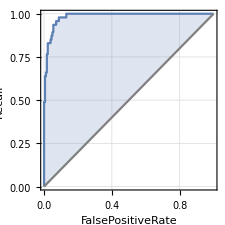

```mathematica
Block[{img},
img = First@Show[m["ROCCurve"][yes], ImageSize-> 8cm];
Export[FileNameJoin[{thesisImages, "new-process_track-select_roc.pdf"}],img];
img
]
```